# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order2_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles[[1]]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse2\0) Fitting Theta, Masking and Roughness\Export

# Parametrization of Θ

```mathematica
paramsTheta = Table[ Table[rawFiles[[albedo]][[j]][[i]][[1]],{j,1,resY},{i,1,resX}],{albedo,1,resZ}];
MatrixForm[paramsTheta];
```

```mathematica
Show[Table[ListPlot3D[paramsTheta[[albedo]],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,π/2}}], {albedo,1,resZ}]]
```

-Graphics3D-

No surprise there : the diffuse lobe is almost static and has no prefered direction so θ = 0 ⟹ One less parameter to worry about!
NOTE: Now it’s completely flat because I really constrained the θ parameter to 0 in subsequent simulations.

# Parametrization of the Lobe’s Masking Parameter m

```mathematica
paramsMasking = Table[Table[rawFiles[[albedo]][[j]][[i]][[5]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsMasking[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsMasking[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsMasking[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}],
ListPlot3D[paramsMasking[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}]]
```

-Graphics3D-

Without surprise, we can fix that parameter to 0 to avoid bumps in the scale parameters.

# Parametrization of the Lobe’s Roughness Parameter α

Here is our relation between roughness α and lobe exponent η:

```mathematica
roughness2exponent[α_] := 2^(10*(1-α))-1
roughness2exponent[0.95913]
```

0.327489

```mathematica
paramsRoughness = Table[Table[rawFiles[[albedo]][[j]][[i]][[2]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
paramsExponent = Table[Table[roughness2exponent[rawFiles[[albedo]][[j]][[i]][[2]]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsRoughness[[1]],{ PlotRange->{0.85,1.0},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsRoughness[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue]]
ListPlot3D[paramsRoughness[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
ListPlot3D[paramsRoughness[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
```

-Graphics3D-

```mathematica
Show[ Table[ListPlot3D[paramsRoughness[[albedo]],{ PlotRange->{0.85,1.0},AxesLabel->{"θ","α"}},PlotStyle->Hue[albedo/(1*resZ)]],{albedo,1,resZ-4}]]
```

-Graphics3D-

### Representative Shape

It appears the lobe roughness is pretty much identical for different albedos so we could build an average plot:

```mathematica
avgParamsRoughness=1/4 Sum[paramsRoughness[[albedo]],{albedo,1,4}];
ListPlot3D[avgParamsRoughness,PlotRange->{0.85,1}]
```

-Graphics3D-

-Graphics3D-

Now, by averaging a few “roughness lines” in the middle of the surface, we can obtain an average plot of α as a function of surface’s α_s alone (we ignore the dependency on θ):

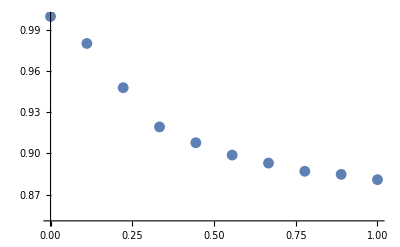

```mathematica
avgRoughness=Table[{1-(j-1)/(resY-1),1/16 Sum[avgParamsRoughness[[j]][[i]],{i,1,16}]},{j,1,resY}];
ListPlot[avgRoughness,PlotRange->{0.85,1}]
```

### Choosing the Model

1-0.2687 α+0.153596 α^2

(a→0.
b→-0.2687
c→0.153596
d→0.)

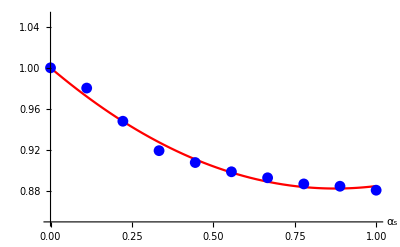

```mathematica
Clear[a,b,c,d]
modelAlpha=0*a+b*u-c*u^2;
modelAlpha=1+b*u+c*u^2+0*d*u^3;
fittingAlpha = FindFit[ avgRoughness,{modelAlpha},{a,b,c,d},u ];
fAlpha[α_]=Evaluate[modelAlpha/.fittingAlpha/.u->α]
MatrixForm[fittingAlpha]
MatrixForm[fittingAlpha/.fittingAlpha];
Show[
Plot[fAlpha[α],{α,0,1},PlotRange->{0.85,1.05},PlotStyle->Red,AxesLabel->{"α_s",}],
ListPlot[avgRoughness,PlotRange->{0.85,1.05} , PlotStyle->Blue,AxesLabel->{"α_s",}]
]
```

#### Modeling the exponents

```mathematica
Show[ Table[ListPlot3D[roughness2exponent[paramsRoughness[[albedo]]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Hue[albedo/(4*resZ)]],{albedo,1,resZ}]];
Show[
ListPlot3D[paramsExponent[[1]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsExponent[[2]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsExponent[[3]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Green]
]
Show[
ListPlot3D[roughness2exponent[1/3 Sum[paramsRoughness[[i]],{i,1,3}]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[1/3 Sum[paramsExponent[[i]],{i,1,3}],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Blue]
]
```

-Graphics3D-

-Graphics3D-

### Representative Shape

There seems to be a nice model to fit for the exponent depending on the surface’s θ and roughness α_s.
First we will try and model the most obvious tendency of the surface: its curvy slope depending on roughness α_s.
For this, let’s use the slope at its maximum value when θ = 0°

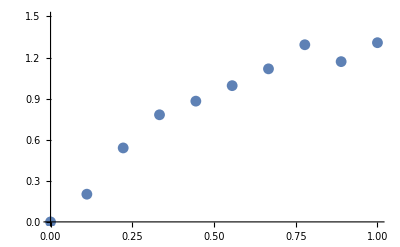

```mathematica
averageParamsExponent = 1/3 Sum[paramsExponent[[i]],{i,1,3}];
dataMaxExponent=Table[{1-(j-1)/(resY-1),averageParamsExponent[[j]][[1]]},{j,1,resY}];
ListPlot[dataMaxExponent,PlotRange->{0,1.5}]
```

### Choosing the Model

2.5958 α-1.32697 α^2

(a→0.
b→2.5958
c→-1.32697
d→0.)

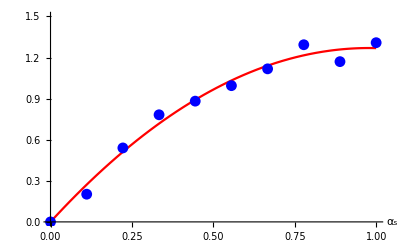

```mathematica
Clear[a,b,c,d]
modelEta=0*a+b*u-c*u^2;
modelEta=0*a+b*u+c*u^2+0*d*u^3;
fittingEta = FindFit[ dataMaxExponent,{modelEta},{a,b,c,d},u ];
fEta[α_]=Evaluate[modelEta/.fittingEta/.u->α]
MatrixForm[fittingEta]
MatrixForm[modelEta/.fittingEta];
Show[
Plot[fEta[α],{α,0,1},PlotRange->{0,1.5},PlotStyle->Red,AxesLabel->{"α_s",}],
ListPlot[dataMaxExponent,PlotRange->{0,1.5} , PlotStyle->Blue,AxesLabel->{"α_s",}]
]
```

```mathematica
NumberForm[N[b/.fittingEta[[2]]],16]
NumberForm[N[c/.fittingEta[[3]]],16]
NumberForm[N[d/.fittingEta[[4]]],16]
```

2.59580242587643

-1.32697372185433

0.

### Applying the Model

Now, let’s try and apply the model with different maximum amplitudes to try and match all the surface, this time depending on θ:

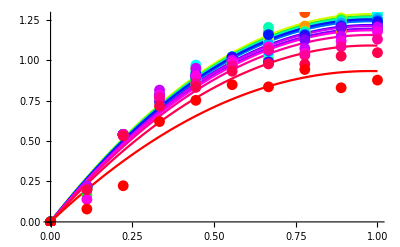

```mathematica
modelEta2=amp * fEta[α];
dataExponents=Table[Table[{1-(j-1)/(resY-1),averageParamsExponent[[j]][[i]]},{j,1,resY}],{i,1,resX}];

fittingAmp = Table[FindFit[ dataExponents[[i]],{modelEta2},{amp},α ],{i,1,resX}];
MatrixForm[fittingAmp];
Show[
Table[Plot[amp*fEta[α]/.fittingAmp[[i]],{α,0,1},PlotStyle->Hue[i/(1*resX)]],{i,1,resX}],
Table[ListPlot[dataExponents[[i]],PlotStyle->Hue[i/(1*resX)]],{i,1,resX}]
]
```

Fitting for all possible θ is okay-ish... Let’s see the amplitude as a function of cos(θ) now:

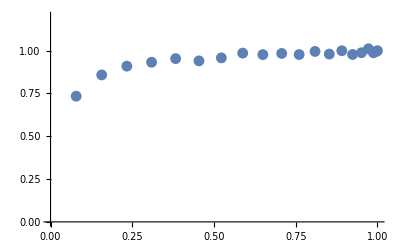

```mathematica
dataAmpCosTheta=Table[{Cos[(i-1)/resX*π/2],amp/.fittingAmp[[i]]},{i,1,resX}];
ListPlot[dataAmpCosTheta,PlotRange->{0,1.2}]
```

Here we have the choice to either fit amplitude as a function of cos(θ) or assume a constant amplitude of 1 all along and simply depend on α_s only...
I think the effort is quite futile since we’re after a simple model so let’s stick to the lobe roughness σ only being dependent on the surface roughness σ_s.

Final Expression

We finally have the following expressions for lobe roughness α and lobe exponent η :

	α(α_s)= 1-0.2687 α+0.153596 α^2
	η(α_s)=2.5958 α-1.32697 α^2

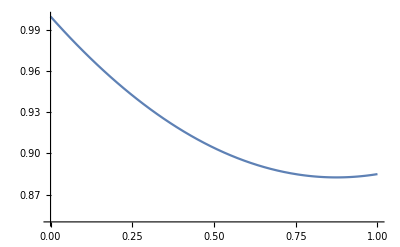

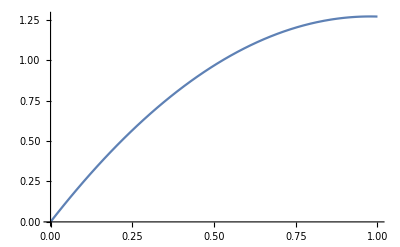

```mathematica
fAlpha[α_]= 1-0.2686997865426857 α+0.1535959296279097 α^2;
fEta[α_]=2.595802425876429 α-1.3269737218543278 α^2;
Plot[fAlpha[α],{α,0,1},PlotRange->{0.85,1.0}]
Plot[fEta[α],{α,0,1}]
```